## sqrt(2)3 Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=(100#1+10#2+#3)&@@@Partition[RealDigits[Sqrt[2],10,30002][[1,2;;]],3];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{0.0970533,0.975118}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→1,5→991,4→1499,11→197,3→2075,8→402,7→507,10→212,17→57,16→70,2→2260,6→689,9→335,23→12,21→28,24→19,38→1,15→77,12→151,14→101,13→121,20→30,25→13,31→4,28→9,33→6,18→40,42→1,39→1,47→1,30→5,19→26,26→10,35→7,29→6,22→18,34→2,32→4,27→8,50→1,44→1,41→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

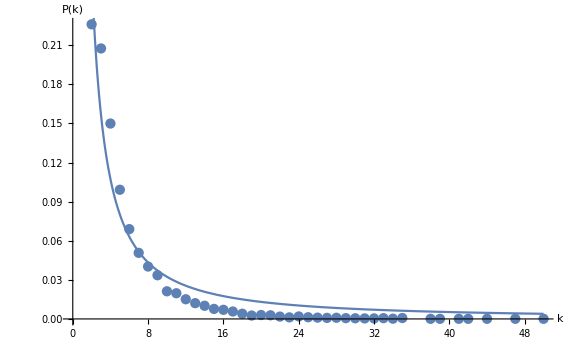
{{C→0.658302,γ→1.30866},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→1,4→1307,3→2135,8→301,2→3622,5→898,6→653,10→144,7→448,11→91,14→33,9→188,16→18,12→71,17→9,13→40,20→4,15→20,18→8,19→4,22→2,21→1,23→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

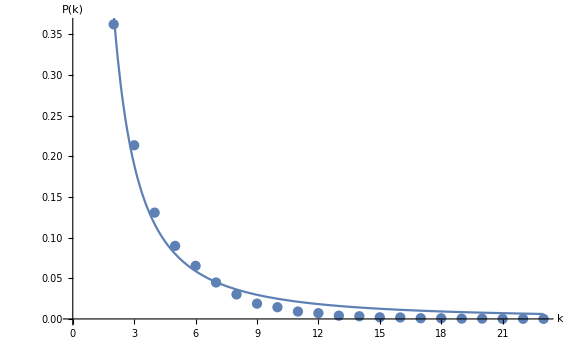
{{C→1.21085,γ→1.68828},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```